# PA4

## Generating test files

These tests generates symmetric (numbers with similar lengths) test cases.

### Multiplication

```mathematica
Export["1.txt",Prepend[#,Length[#]]&@Flatten[Table[{x, y, x y}/.{x->RandomInteger[{10^#1,10^(#1+1)}], y->RandomInteger[{10^(#1),10^(#1+1)}]},100]&/@Range[1,100,2],1]]
```

### Division

```mathematica
Export["1.txt",Prepend[#,Length[#]]&@Flatten[Table[{x, y, Floor[x/y]}/.{x->RandomInteger[{10^#1,10^(#1+1)}], y->RandomInteger[{10^#1,10^(#1+1)}]},20]&/@Range[1,100,2],1]]
```

Other tests are generated using similar code.

## Benchmark and Algorithm Choosing

### Multiplication

```mathematica
fft =Mean/@Partition[Flatten@Import["fft.txt","Data"],100];
```

```mathematica
karatsuba =Mean/@Partition[Flatten@Import["karatsuba.txt","Data"],100];
```

```mathematica
long = Mean/@Partition[Flatten@Import["long.txt","Data"],100];
```

```mathematica
toom3calll =Mean/@Partition[Flatten@Import["toom3_calll.txt","Data"],100];
```

```mathematica
toom3callk =Mean/@Partition[Flatten@Import["toom3_callk.txt","Data"],100];
```

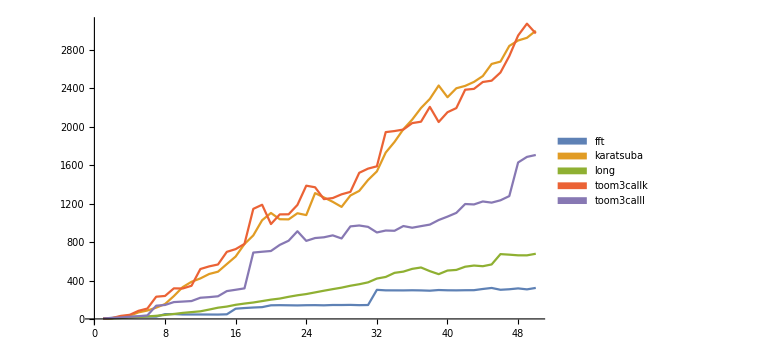

```mathematica
ListPlot[{fft,karatsuba,long,toom3callk,toom3calll},PlotLegends->SwatchLegend[{{"fft","karatsuba","long","toom3callk","toom3calll"}}],Joined->True,ImageSize->Large]
```

The algorithm implemented are:
Long multiplication: O(n^2) 
Karatsuba multiplication: O(n^1.585) 
Toom-Cook 3 Way multiplication: O(n^1.465) 
Fast Fourier Transform Multiplication: O(n log(n)) 
However, FFT and long multiplication outproformed others(maybe due to optimization problems).

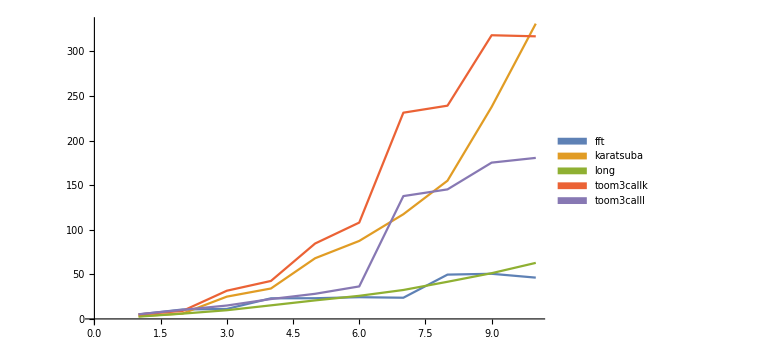

```mathematica
ListPlot[{fft,karatsuba,long,toom3callk,toom3calll}[[All,1;;10]],PlotLegends->SwatchLegend[{{"fft","karatsuba","long","toom3callk","toom3calll"}}],Joined->True,ImageSize->Large]
```

Hence for operand less than 10^12, long multiplication is used, and fft is used for larger multiplications.

### Division

```mathematica
longdiv =Mean/@Partition[Flatten@Import["long.txt","Data"],20];
```

```mathematica
newtondiv =Mean/@Partition[Flatten@Import["newton.txt","Data"],20];
```

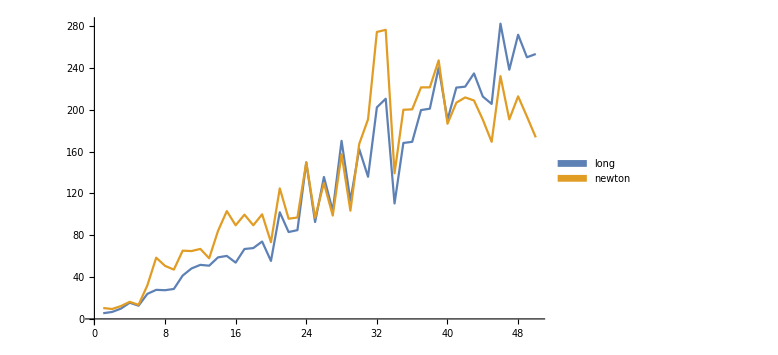

```mathematica
ListPlot[{longdiv,newtondiv},PlotLegends->SwatchLegend[{{"long","newton"}}],Joined->True,ImageSize->Large]
```

```mathematica
datalong = Transpose@{Range[50],longdiv};
```

```mathematica
datanewton = Transpose@{Range[50],newtondiv};
```

```mathematica
lmlong = LinearModelFit[datalong,x,x]
```

FittedModel[-18.3665+5.58673 x]

```mathematica
lmnewton = LinearModelFit[datanewton,x,x]
```

FittedModel[13.7592+4.57007 x]

```mathematica
Solve[Normal@lmlong==Normal@lmnewton,x]
```

{{x→31.5994}}

Hence long division is used for operands less than 10^62, and Newton division is used for larger numbers.